Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.1 (Approssimazione di funzione con il suo sviluppo di Taylor).

### Testo dell’esercizio

Come sono approssimate le funzioni sin(x) e 1/(1+x^2) dai loro polinomi di Taylor di ordine crescente?

### Svolgimento

Vogliamo tracciare una griglia dei grafici con passo crescente tra le righe di f(x)=sin(x) e g(x)=1/(1+x^2) contro il loro sviluppo in serie di McLaurin, ossia lo sviluppo di Taylor centrato in x=0.

```mathematica
f=Sin;
g= 1/(1+#^2)&;
```

Fissiamo l’intervallo [-10,10] per uno studio più agevole.

```mathematica
GraphicsRow[{Plot[Sin[x],{x,-10,10}],Plot[g[x],{x,-10,10},PlotRange->Full]}]
```

Possiamo notare che l’immagine di entrambe le funzioni è contenuta nell’intervallo [-1,1].
Fissiamo PlotRange→{-1.5,1.5} per lasciare del padding attorno ai grafici.

```mathematica
rows[f_,x_,start_,step_,len_]:=Table[Plot[{f[x] , Series[f[x],{x,0,k}]//Normal//Evaluate},{x,-10,10},PlotLabel->k,PlotRange->{-1.5,1.5}],{k,start,start+len step,step}]
```

Creata una funzione che genera una lista con il grafico di f(x) e del suo polinomio di McLaurin all’ordine k-esimo nell’opportuna posizione, aumentando di ordine con step costante tra grafico e grafico,

```mathematica
gridd[f_,x_,height_,length_]:= Table[rows[f,x,st[length,k],k,length],{k,1,height}]
```

la utilizziamo per creare una griglia (lista di liste) di grafici con step che aumenta all’aumentare della riga. Per fare ciò, serve calcolare con quale ordine deve cominciare ogni riga. Lo si può definire con una funzione ricorsiva

st[length_, 1] = 1;
st[length_, k_] := st[length, k - 1] + (length + 1) k

Che dà luogo alla formula chiusa (molto migliore in termini di computazione) :

```mathematica
st[length_,k_]:=1+(length+1)/2(-2+k+k^2)
```

Tracciamo i grafici relativi ad f^

```mathematica
GraphicsGrid[gridd[f,x,4,4],ImageSize->Full]
```

e i grafici relativi a g.

```mathematica
GraphicsGrid[gridd[g,x,5,4],ImageSize->Full]
```

Si notano subito differenze nel modo in cui gli sviluppi di Taylor convergono alle 2 funzioni al variare di n∈ℕ: ciò è dovuto al fatto che le derivate n-esime della funzione di Runge (ossia g) sono “grandi” in norma-∞ su ogni compatto di ℝ. Nell’intervallo [-10,10], lo sviluppo di f al trentesimo ordine è indistinguibile da f, mentre la differenza tra g e il suo sviluppo è ben visibile persino al centesimo ordine.
Possiamo ottenere ulteriori informazioni a riguardo tracciando il punto dove lo sviluppo si distanzia dalla funzione più di un certo ε. Sfruttando le simmetrie delle due funzioni, possiamo restringerci alla semiretta positiva.

```mathematica
dst[f_,n_] := Abs[f[x]-Evaluate@Normal[Series[f[x],{x,0,n}]]]
```

```mathematica
convf=FindRoot[dst[f,#]==0.01,{x,#-2}]&
```

```mathematica
convg=FindRoot[dst[g,#]==0.01,{x,#/55}]&
```

Otteniamo

```mathematica
GraphicsRow [{ListPlot[x/.convf/@Range[1,50,2],PlotRange->{0,20}],ListPlot[x/.convg/@Range[1,50,2],PlotRange->{0,1}]},ImageSize->Large]
```

Tracciando le distanze in funzione dell’ordine del polinomio, si nota che lo sviluppo del seno rimane ad una distanza ≤ 0.01 dal seno per intervalli arbitrariamente grandi, mentre lo sviluppo della funzione di Runge non sembra eccedere |x|≤1.
Utilizzando mezzi esterni abbiamo verificato che effettivamente lo sviluppo di McLaurin della funzione di Runge non converge uniformemente alla stessa fuori da [-1,1], ossia che pur essendo 𝒞^∞ non è analitica. Si possono comunque ottenere informazioni sulla convergenza: studiamo, quindi, la convergenza puntuale della coppia di funzioni dal rispettivo sviluppo centrato in 0 nel punto x=1/2.

```mathematica
puntf=dst[f,#]/.x->1/2&;
puntg=dst[g,#]/.x->1/2&;
```

Chiaramente le distanze decrescono molto velocemente: ne tracciamo, quindi, il logaritmo.

```mathematica
GraphicsRow [{ListLogPlot[puntf/@Range[1,30,2]],ListLogPlot[puntg/@Range[1,30,2]]},ImageSize->Large]
```

Ora si può notare che le due convergenze puntuali hanno lo stesso andamento (esponenziale) e che il seno è significativamente più veloce: la distanza è nell’ordine di 10^-50 dal seno e di 10^-10dalla funzione di Runge sviluppando le rispettive approssimazioni fino al trentesimo ordine.

## Esercizio 1.2 (Algebra & Coreografie).

### Testo dell’esercizio

Le tre radici del polinomio x^3+b x+c dipendono dai coefficienti b e c e sono genericamente complesse (e distinte, ma per speciali valori di b e c una o tutte possono essere reali e due o tutte possono coincidere).
Per ogni scelta di b e c, le radici sono dunque 3 (o 2 o 1) punti nel piano complesso. Se si fa muovere il punto (b,c)∈ℝ^2 lungo una curva Γ in ℝ^2, le radici si muovono lungo tre curve (che possono avere delle intersezioni) nel piano complesso ℂ.
Si chiede di generare un filmato che mostra, affiancati, il moto del punto (b,c)∈ℝ^2 lungo una curva e il corrispondente moto (o “danza”) delle radici in ℂ.

### Svolgimento

Innanzitutto alleggeriamo la notazione: scriviamo il polinomio assegnato come funzione di x e dei parametri b e c e creiamo una funzione che calcoli le radici al variare degli stessi;

```mathematica
P[b_,c_,x_]:= x^3+b x + c
```

```mathematica
rads[a_,b_]:= x/.NSolve[P[a,b,x]==0,x]
```

con un’altra funzione trasformiamo le radici complesse in vettori bidimensionali reali;

```mathematica
C2R2[a_,b_,k_]:= {Re[rads[a,b]⟦k⟧],Im[rads[a,b]]⟦k⟧}
```

disegniamo, poi, i 3 punti in un quadrato, senza specificarne la dimensione, così da permettere una visualizzazione del risultato coerente ad ogni grafico passando un range appropriato al variare della curva scelta in ℝ^2.

```mathematica
pointsRange[a_,b_,range_]:= Graphics[
{PointSize[Large],Red,Point[C2R2[a,b,1]],Green,Point[C2R2[a,b,2]],Blue,Point[C2R2[a,b,3]]},
PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None
]
```

Abbiamo deciso di creare i punti con Graphics e non con ListPlot per due semplici motivi:

ci è parso più consono alla natura grafica del progetto;

semplifica la gestione delle direttive grafiche, come ad esempio i tre colori distinti.

Scriviamo ora una funzione che crea due grafici, il primo con il supporto della curva scelta ed il punto che si muove lungo di essa, il secondo con le 3 soluzioni e la “scia” delle stesse, il tutto colorato opportunamente.

```mathematica
dance[t_,a_,b_,γ1_,γ2_,range_]:=GraphicsRow[
{
ParametricPlot[{γ1[θ],γ2[θ]},{θ,a,b},Ticks->{None,None},PlotStyle->Black,Epilog->{Purple,PointSize[Large],Point[{γ1[t],γ2[t]}]}],
Show[
pointsRange[γ1[t],γ2[t],range],
ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],1],{τ,a,t,0.01}],PlotStyle->Red],
ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],2],{τ,a,t,0.01}],PlotStyle->Green],
ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],3],{τ,a,t,0.01}],PlotStyle->Blue]
]
}
]
```

Abbiamo utilizzato ListLinePlot, anche se sarebbe stato forse più corretto ListCurvePathPlot; tuttavia la resa grafica è simile (per campionamenti sufficientemente fitti) e l’interpolazione lineare riduce di molto i tempi di calcolo.

```mathematica
γ1[t_]:=Cos[t]
γ2[t_] := Sin[t]
```

Definiamo le componenti di una curva parametrizzata (in questo caso una circonferenza), poi manipoliamo la “danza” sulla circonferenza.

```mathematica
Manipulate[dance[t,0,2π,γ1,γ2,1.5],{t,0,2π}]
```

Il Manipulate è lento, ma permette di vedere approssimativamente il risultato dell’animazione. Creiamo una funzione che ci consenta di esportare rapidamente delle animazioni come looping GIF a 30 fotogrammi al secondo,

```mathematica
exportmygif[list_,name_]:= Export[NotebookDirectory[]<>name<>".gif",list,ImageSize->Large,"DisplayDurations"->(1/30&/@Range[Length[list]]),"AnimationRepetitions"->∞]
```

di cui lasciamo un esempio che mostra la danza sulla circonferenza (animazione di 5 secondi a 30fps).

```mathematica
circleframes = Table[dance[t,0,2π,γ1,γ2,1.5],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[circleframes,"circle"]
```

Sembra naturale guardare i risultati della funzione dance anche su un’ellisse di parametri (2,1).

```mathematica
λ1[t_]:=2Cos[t]
λ2[t_] := Sin[t]
```

```mathematica
Manipulate[dance[t,0,2π,λ1,λ2,2],{t,0,2π}]
```

```mathematica
ellipseframes = Table[dance[t,0,2π,λ1,λ2,2],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[ellipseframes,"ellipse"]
```

Consigliamo vivamente di guardare alla sezione successiva, come introduzione alla sezione Extra, oltre che per la bellezza delle immagini prodotte.

### Media 2D

Abbiamo voluto provare la funzione con alcune curve note, di cui lasicamo solo l’immagine con il tracciato delle soluzioni ed i comandi per esportare la relativa animazione. È stato studiato ulteriormente il caso della cardioide nella sezione Extra, in quanto sembrava particolarmente interessante.

#### Spirale di Archimede (a=0, b=1)

```mathematica
arcx[t_]:= t Cos[t]
arcy[t_]:=t Sin[t]
```

```mathematica
dance[3π,0,3π,arcx,arcy,3]
```

```mathematica
archiframes = Table[dance[t,0,3π,arcx,arcy,3],{t,Subdivide[0,3π,150]}];
```

```mathematica
exportmygif[archiframes,"archimede"]
```

#### Spirale logaritmica (β=1, κ=-1)

```mathematica
logx[t_]:= ⅇ^-t Cos[t]
logy[t_]:=ⅇ^-t Sin[t]
```

```mathematica
Dance[10,-10,10,logx,logy,1]
```

```mathematica
logframes = Table[Dance[t,-10,10,logx,logy,1],{t,Subdivide[-10,10,150]}];
```

```mathematica
exportmygif[logframes,"logspiral"]
```

#### Cardioide

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
```

```mathematica
dance[2π,0,2π,cardx,cardy,1.5]
```

```mathematica
cardframes = Table[dance[t,0,2π,cardx,cardy,1.5],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[cardframes,"cardioid"]
```

#### Lemniscata di Bernoulli

```mathematica
lemx[t_]:= Sin[t]/(1+Cos[t]^2)
lemy[t_]:=(Sin[t]Cos[t])/(1+Cos[t]^2)
```

```mathematica
dance[2π,0,2π,lemx,lemy,1.2]
```

```mathematica
lemnframes = Table[dance[t,0,2π,lemx,lemy,1.2],{t,0,2π,0.05}];
```

```mathematica
exportmygif[lemnframes,"lemniscus"]
```

#### Porzione di folium di Cartesio

```mathematica
folx[t_]:= t(t-1)
foly[t_]:=t (t-1)(2t-1)
```

```mathematica
dance[1.5,-0.5,1.5,folx,foly,1]
```

```mathematica
foliumframes = Table[dance[t,-0.5,1.5,folx,foly,1],{t,Subdivide[-0.5,1.5,150]}];
```

```mathematica
exportmygif[foliumframes,"folium"]
```

### Extra (Cardioidi e Lemniscate)

Poiché, facendo variare i parametri su una cardioide, le soluzioni producono quel che sembra una lemniscata, abbiamo provato a “dimostrare” tale congettura. Procediamo con una verifica grafica, riportando la parametrizzazione della cardioide.

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
```

Creiamo il grafico con la traccia delle soluzioni a ciclo completato.

```mathematica
lemnimaybe =Show[{ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],1],{τ,0,2π,0.05}],PlotStyle->Red,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],2],{τ,0,2π,0.05}],PlotStyle->Green,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],3],{τ,0,2π,0.05}],PlotStyle->Blue,PlotRange->{{-1,1},{-1.5,1.5}}]}]
```

Cerchiamo di capire quale sia la scala della figura, ossia quali siano i massimi rispetto alle due coordinate. Possiamo cercarli limitatamente al tracciato del punto verde al variare di t.

```mathematica
Max[Table[C2R2[cardx[τ],cardy[τ],2]⟦1⟧,{τ,0,2π,0.01}]]
Max[Table[C2R2[cardx[τ],cardy[τ],2]⟦2⟧,{τ,0,2π,1/100}]]
```

Dinanzi a tali risultati, approssimiamo il secondo numero a √2. Per utilizzare la parametrizzazione della lemniscata di Bernoulli, la ruotiamo di π/2 e la dilatiamo opportunamente nelle direzioni degli assi, di modo che combaci con la curva sopra. Calcoliamo il valore inferiore e definiamo la lemniscata.

```mathematica
m=Max[Table[(Sin[t]Cos[t])/(1+Cos[t]^2),{t,0,2π}]];
```

```mathematica
Lemn = ParametricPlot[{1/(2m)(Sin[t]Cos[t])/(1+Cos[t]^2),√2 Sin[t]/(1+Cos[t]^2)},{t,0,2π},PlotStyle->{Purple,Dashed,Thick}];
```

Ora tracciamo i due grafici sovrapposti.

```mathematica
Show[{lemnimaybe,Lemn},ImageSize-> Large]
```

Dal momento che nel grafico sembrano coincidere, cerchiamo di darne una dimostrazione. Vogliamo dimostrare che

ove ℒ è la lemniscata e x_1, x_2, x_3 sono le tre radici di x^3+a(t) x+b(t), con a(t) e b(t) che variano sulla cardioide.

Ciò è vero se e solo se, posto z(τ)=lemn_x(τ)+ⅈ lemn_y(τ), è vero che per ogni τ∈[0,2π] esiste t∈[0,2π] tale che (z(τ))^3+a(t)z(τ)+b(t)=0. Definiamo una funzione che restituisca la norma del polinomio calcolato sulle coordinate della cardioide; ciò è necessario perché, quando calcoleremo il polinomio più avanti, restituirà principalmente valori complessi — e a noi interessa visualizzare i risultati come grafico di una funzione ℝ→ℝ.

```mathematica
Pcard[t_,x_]:= Norm[P[Cos[t](1+Cos[t]),Sin[t] (1+Cos[t]),x]]
```

Calcoliamo i punti sulla lemniscata come numeri complessi,

```mathematica
cmplxL[t_]:= 1/2(1+Cos[1]^2)/(Cos[1]Sin[1])(Sin[t]Cos[t])/(1+Cos[t]^2)+ I √2 Sin[t]/(1+Cos[t]^2)
```

e osserviamo i grafici nella variabile τ facendo variare t con uno slider.

```mathematica
Manipulate[Plot[Pcard[t,cmplxL[τ]],{t,0,2π},PlotRange->{0,1.5}],{τ,0,2π}]
```

Si può vedere che ogni funzione generata ha almeno uno 0 (con le dovute approssimazioni dovute alla limitata precisione delle funzioni e all’approssimazione “a occhio” della parametrizzazione della lemniscata). Questa dimostrazione non è rigorosa né particolarmente elegante, ma permette di congetturare la correttezza di un risultato simile, ossia scalando la lemniscata di un fattore più preciso.

### Generalizzazione a curve in ℝ^3

Viene naturale porsi il medesimo problema sul polinomio x^3+ax^2+bx+c con a, b, c che variano lungo una curva in ℝ^3. Lo svolgimento è il medesimo:

```mathematica
p3D[a_,b_,c_,x_]:= x^3+a x^2+b x + c
```

```mathematica
rads3D[a_,b_,c_]:= x/.NSolve[p3D[a,b,c,x]]
```

```mathematica
c2r2[a_,b_,c_,k_]:= {Re[rads3D[a,b,c][[k]]],Im[rads3D[a,b,c]][[k]]}
```

```mathematica
pointsRange3D[a_,b_,c_,range_]:=Graphics[
{
PointSize[Large],
Red,Point[c2r2[a,b,c,1]],
Green,Point[c2r2[a,b,c,2]],
Blue,Point[c2r2[a,b,c,3]]
},
PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None
]
```

```mathematica
dance3D[t_,a_,b_,i_,j_,k_,range_]:= GraphicsRow[
{
Show[
ParametricPlot3D[{i[θ],j[θ],k[θ]},{θ,a,b},PlotStyle->Black,Ticks->None],Graphics3D[{Purple,PointSize[Large],Point[{i[t],j[t],k[t]}]}]
],
Show[
pointsRange3D[i[t],j[t],k[t],range],
ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],1],{τ,a,t,0.01}],PlotStyle->Red],ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],2],{τ,a,t,0.01}],PlotStyle->Green],ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],3],{τ,a,t,0.01}],PlotStyle->Blue]
]
}
]
```

```mathematica
i[t_]:= Cos[t]
j[t_]:= Sin[t]
k[t_]:= t
```

Proviamo la funzione su un’elicoide in un quadrato 6×6.

```mathematica
Manipulate[dance3D[t,0,4π,i,j,k,4],{t,0,4π}]
```

Benché questa implementazione non abbia nulla di troppo diverso dalla versione 2D, essa offre la possibilità di creare nuove “danze” in tre dimensioni (sezione Media3D).

```mathematica
elicoidframes = Table[dance3D[t,0,4π,i,j,k,4],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[elicoidframes,"elicoid"]
```

### Media 3D

Messa a punto la funzione in 3D, lasciamo immagini e comandi come sopra per alcune curve in ℝ^3 note.

#### Parte di nodo di LissaJous (a=b=c=ϕ=ψ=n=1, m=2)

```mathematica
lisx[t_]:= Sin[t]
lisy[t_]:= Sin[t+1]
lisz[t_]:= Sin[2t+1]
```

```mathematica
dance3D[10,-10,10,lisx,lisy,lisz,1.5]
```

```mathematica
lissaframes = Table[dance3D[t,-10,10,lisx,lisy,lisz,1.5],{t,Subdivide[-10,10,150]}];
```

```mathematica
exportmygif[lissaframes,"lissajous"]
```

#### Bordo della finestra di Viviani

```mathematica
vivx[t_]:= 1+Cos[t]
vivy[t_]:= Sin[t]
vivz[t_]:= 2Sin[t/2]
```

```mathematica
dance3D[4π,0,4π,vivx,vivy,vivz,1.5]
```

```mathematica
vivianframes = Table[dance3D[t,0,4π,vivx,vivy,vivz,1.5],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[vivianframes,"viviani"]
```

#### Cucitura di una palla da tennis (a=b=c=1):

```mathematica
tenx[t_]:= Cos[t]+Cos[3t]
teny[t_]:= Sin[t]-Sin[3t]
tenz[t_]:= Sin[2t]
```

```mathematica
dance3D[4π,0,4π,tenx,teny,tenz,1.5]
```

```mathematica
tennisframes = Table[dance3D[t,0,4π,tenx,teny,tenz,1.5],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[tennisframes,"tennisball"]
```

## Esercizio 1.3 (Teorema dei numeri primi).

### Testo dell’esercizio

Il teorema dei numeri primi afferma che le funzioni π(n), n/(log(n)), li(n) sono asintotiche per n→∞. Investigare numericamente quest’affermazione.

### Svolgimento

Ricorrendo al risolutore di limiti interno a Mathematica, possiamo intravedere l’asintoticità per n→∞.

```mathematica
{
Limit[PrimePi[n]/(n/Log[n]),n->∞],
Limit[PrimePi[n]/LogIntegral[n],n->∞]
}
```

Occorre precisare che ciò non significa che il modulo della differenza tra due delle funzioni in esame sia infinitesimo. Come si vede nel grafico seguente, la differenza in valore assoluto tra π(n) e n/(log(n)) è tendenzialmente crescente. Dal grafico, però, non è chiaro quale α>0 sia tale che n^α sia asintotico a |π(n)-n/(log(n))| — né, in realtà, sono presenti elementi che assicurino l’esistenza di un tale α.
D’ora in poi, tutti i grafici saranno divisi in “porzioni”: il parametro k∈ℕ indica l’ordine di grandezza in base 10 da cui la parte di grafico comincia.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-x/Log[x]],
x^α
},
{x,10^k,10^(k+3)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-x/Log[x]]],TraditionalForm[x^α]},Ticks->{N@(10^Range[k,k+3]),Automatic}(*La N impedisce che i numeri sotto i tick compaiano per esteso anche quando troppo lunghi.*)
],
{k,Range[9]},(*Questa sintassi permette di ottenere un controllo a tendina anziché a slider.*)
{α,0.1,1}
]
```

Confrontando π(n) con li(n), seppur con oscillazioni più pronunciate, si ottiene ugualmente che la differenza in valore assoluto tra le due funzioni non è infinitesima, ma tendente a ∞ per n→∞. Anche in questo caso non è facile individuare “ad occhio” l’esponente β>0, se esiste, tale che n^β sia asintotico a |π(n)-li(n)|.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-LogIntegral[x]],
x^β
},
{x,10^k,10^(k+2)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-LogIntegral[x]]],TraditionalForm[x^β]},Ticks->{N@(10^Range[k,k+2]),Automatic}
],
{k,Range[10]},
{β,0.3,.45}
]
```

Il grafico seguente indaga “visivamente” l’asintoticità di π(n) e n/(log(n)), ovvero mostra se il rapporto tra le due funzioni tende a 1. Si può notare che il rapporto è definitivamente decrescente ed inferiormente limitato da 1, ma il decadimento è molto lento.

```mathematica
Manipulate[
LogLogPlot[
PrimePi[x]/(x/Log[x]),
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[Defer@(PrimePi[x]/(x/Log[x]))]},PlotRange->{.99,1.3}
],
{k,Range[0,9]}
]
```

L’asintoticità di π(n) e li(n), invece, è molto più evidente a partire dal grafico: già per n>10^5 il rapporto tra le due funzioni è “molto vicino” a 1.

```mathematica
Manipulate[
LogLogPlot[
LogIntegral[x]/PrimePi[x],
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[PrimePi[x]/LogIntegral[x]]},PlotRange->{0.999,1.5}
],
{k,Range[9]}
]
```

Un’altra funzione da considerare per verificare l’asintoticità di π(n) e n/(log(n)) è l’oscillazione relativa (π(n)-n/(log(n)))/(π(n)), che però è approssimabile con la più semplice (π(n))/(n / log(n))-1, come si vede nei seguenti grafici.

```mathematica
Manipulate[
LogLogPlot[{(PrimePi[x]-x/Log[x])/PrimePi[x],PrimePi[x]/(x/Log[x])-1},
{x,10^k,10^(k+3)},
Ticks->{N@(10^Range[k,k+3]),Automatic},PlotRange->{0.01,0.3}
],
{k,Range[9]}
]
```

Mostriamo, dunque, il grafico della funzione più semplice.

```mathematica
Manipulate[
LogLogPlot[PrimePi[x]/(x/Log[x])-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+3]),Automatic},PlotRange->{0.01,0.3}
],
{k,Range[9]}
]
```

È possibile notare che tale funzione è decrescente, ma anch’essa ha un decadimento molto lento.

Analogamente, vediamo il grafico di (li(n))/(π(n))-1.

```mathematica
Manipulate[
LogLogPlot[LogIntegral[x]/PrimePi[x]-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic}
],
{k,Range[9]}
]
```

Il decadimento di questa funzione è molto più pronunciato, ma non si riesce ugualmente ad approssimare tale decadimento con una potenza adeguata: non solo una potenza che pare approssimare la funzione in una parte del grafico devia nelle altre porzioni, ma le oscillazioni della funzione da studiare rendono il confronto ancora più complicato.

## Esercizio 1.4 (Cicloide).

### Testo dell’esercizio

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata cicloide, di equazioni parametriche

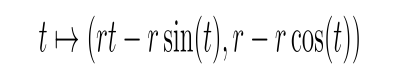

Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che rotola, il punto P su di essa, e la curva descritta da P nel piano.

### Svolgimento

Ogni fotogramma dell’animazione deve contenere due strutture:

la ruota che gira;

la “scia” lasciata da P nel piano.

La ruota è composta da una circonferenza di raggio r che trasla, dal punto P sulla circonferenza che ruota e si sposta rimanendo sulla circonferenza e da due linee – un numero minimo di “raggi” della ruota – che seguono il movimento di P. La scia è una cicloide opportunamente riparametrizzata, mostrata di modo che sembri una “scia luminosa” lasciata da P.
Creiamo dapprima una funzione che computi il grafico ad un istante t dato. Tale funzione permette di scegliere il raggio r della circonferenza, l’angolo in senso orario θ di discostamento di P dal punto “più in basso” della circonferenza, il numero di archi che vogliamo vedere descritti dalla curva intorno allo 0 (funziona meglio con numeri pari) e l’istante t che vogliamo mostrare.

Le coordinate del punto P e dei due “raggi” della ruota sono calcolate applicando una glissorotazione rispetto al caso in cui la circonferenza di raggio r sia centrata nell’origine.

```mathematica
ClearAll[rotolaFrame,rotola,rotolaExport]
```

```mathematica
rotolaFrame[r_,θ_,giri_,t_]:=Show[
Graphics[
{
{
Thick,Hue[0.1,0.1,0.1],
Circle[{t ,r},r]
},
{
Hue[0,0,0.6],
Line[{{t,r}+RotationMatrix[(-(θ+t))/r].{0,-r},{t,r}+RotationMatrix[(-(θ+t))/r+π].{0,-r}}],
Line[{{t,r}+RotationMatrix[(-(θ+t))/r+π/2].{0,-r},{t,r}+RotationMatrix[(-(θ+t))/r-π/2].{0,-r}}]
},
{
Red,PointSize[.007],
Point[{t,r}+RotationMatrix[(-(θ+t))/r].{0,-r}]
}
},
Axes->{True,False},Ticks->{Range[-giri π r,giri π r,IntegerPart[giri/2] π],None},PlotRange->{{-(giri π+1)r,(giri π+1) r},{-.1,2r+0.5}},ImageSize->Full
],
ParametricPlot[
r{u-Sin[u],1-Cos[u]}-{θ,0},
{u,-(giri π+1.01)r,(t+θ)/r},
PlotStyle->{Hue[1,0.5,1]}
]
]
```

```mathematica
rotolaFrame[3,π/3,4,7]
```

In seguito, creiamo un oggetto interattivo per dare un’idea dell’evoluzione della curva.

```mathematica
rotola[r_,θ_,giri_]:=Manipulate[
rotolaFrame[r,θ,giri,t],
{t,-(giri π+1)r,(giri π+1) r}
]
```

```mathematica
rotola[3,π/2,2]
```

Possiamo collezionare un numero sufficiente di immagini per creare una GIF fluida: utilizzando uno standard video consolidato, scegliamo di mostrare 30 fotogrammi al secondo.

```mathematica
rotolaExport[r_,θ_,giri_,secondi_]:=Export[NotebookDirectory[]<>"rotolando.gif",rotolaFrame[r,θ,giri,#]&/@Subdivide[-(giri π+1)r,(giri π+1) r,30secondi],ImageSize->1000,"DisplayDurations"->(1/30&/@Range[30secondi+1]),"AnimationRepetitions"->∞]
```

```mathematica
rotolaExport[2,π/6,4,5]
```

### Approfondimento: ipocicloidi ed epicicloidi

Far rotolare una ruota non su una retta, ma su una circonferenza, genera due curve analoghe alla cicloide, ossia l’ipocicloide (se la ruota rotola internamente) e l’epicicloide (se la ruota rotola esternamente). Qui di seguito si crea una funzione per generare – ed esportare come GIF – epicicloidi ed ipocicloidi generate da ruote che rotolano attorno alla circonferenza unitaria.

```mathematica
epiipoFrame[r_,t_]:=Show[
Graphics[
{
Circle[],
Circle[(1-r){Cos[t],Sin[t]},r],
Circle[(1+r){Cos[t],Sin[t]},r],
Rotate[Line[{(1-r){Cos[t],Sin[t]},{Cos[t],Sin[t]}}],-t/r,(1-r){Cos[t],Sin[t]}],
Rotate[Line[{(1+r){Cos[t],Sin[t]},{Cos[t],Sin[t]}}],t/r,(1+r){Cos[t],Sin[t]}],
{Red,Thick,Rotate[Point[{Cos[t],Sin[t]}],-t/r,(1-r){Cos[t],Sin[t]}]},
{Blue,Thick,Rotate[Point[{Cos[t],Sin[t]}],t/r,(1+r){Cos[t],Sin[t]}]}
},
PlotRange->{{-2,2},{-2,2}}
],
ParametricPlot[{{(1-r)Cos[θ]+r Cos[(1-r)/r θ],(1-r)Sin[θ]-r Sin[(1-r)/r θ]},{(1+r)Cos[θ]-r Cos[(1+r)/r θ],(1+r)Sin[θ]-r Sin[(1+r)/r θ]}},{θ,-0.001,t},PlotStyle->{Red,Blue}]
]
```

La funzione di esportazione a GIF, per poter mostrare sempre un’unica sequenza completa, presuppone che il raggio delle circonferenze sia un numero razionale dell’intervallo (0,1).

```mathematica
epiipoExport[r_,secondi_]:=Export[NotebookDirectory[]<>"epiipocilo.gif",epiipoFrame[r,#]&/@Subdivide[0,2Numerator[r]π,30secondi],ImageSize->Large,"DisplayDurations"->(1/30&/@Range[30secondi+1]),"AnimationRepetitions"->∞]
```

```mathematica
epiipoExport[1/3,4]
```